# Logistic growth

## I. Logistic Equation

The logistic equation (sometimes called the Verhulst model or logistic growth curve) is a model of population growth first published by Pierre Verhulst (1845, 1847). 

N'[t]==(r N[t] (K-N[t]))/K

where r is the Malthusian parameter (rate of maximum population growth) and K is the so-called carrying capacity (i.e., the maximum sustainable population).

N'[t]/K==(r N[t] (1-N[t]/K))/K

Letting x=n/k

x’(t) == r x(t)(1 - x(t)) 

Demonstration.

dN / dt = r N ( 1 − N / K)

Analytic Solution. The logistic equation can be solved by separation of variables:

∫ ( dN / ( N ( 1 - N / K ) ) = ∫ r dt .

In order to evaluate the left hand side we write:

1 / ( N ( 1 - N / K ) = K / ( N ( K - N ) ) = 1 / N + 1 / ( K - N ) ,

hence

∫ dN / N + ∫ dN / ( K - N )  = ∫ r dt ,

ln| N | - ln| K - N | = rt + C ,
 
ln| ( K - N ) / N | =  -rt - C ,
 
| ( K - N ) / N | =  e^(-rt - C) ,

( K - N ) / N = A.e^(-rt)		( A = +/- e^(-C) ).

From here we get :

N = K / ( 1 + A.e^(-rt) )	where 	A = ( K - N_0 ) / N_0 ,

Dividing both sides by K and defining x ≡ N / K.

We finally obtain,

x(t) = 1 / ( 1 + B.e^(-rt) )	where 	B = ( 1 / N_0 ) - 1.

The function x(t) is sometimes known as the sigmoid function.

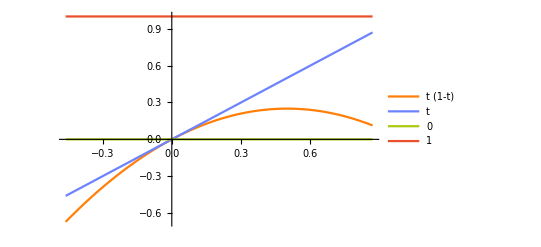

```mathematica
Plot[{1*t*(1 - t), {t, 0, 1}}, {t, -0.46, 0.87}]
```

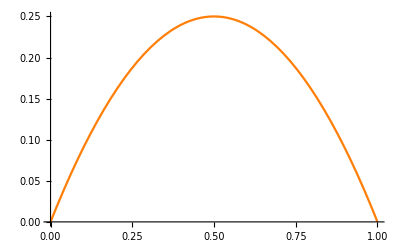

```mathematica
logit = Plot[{(1*t*(1 - t))}, {t, 0, 1}]
```

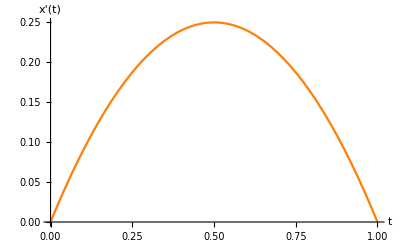

```mathematica
Show[logit,AxesLabel->{HoldForm[t],HoldForm[x'[t]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}, AxesStyle->{Directive[Red,18],Directive[Red,18]}]
```

## II. Sigmoid function

The logistic equation has a solution known has the sigmoid function.

Plot[{1/(1 + (1/0.05 - 1)/E^(1*t)), 1/(1 + (1/0.1 - 1)/E^(1*t)), 1/(1 + (1/0.15 - 1)/E^(1*t))}, {t, 0, 10}]

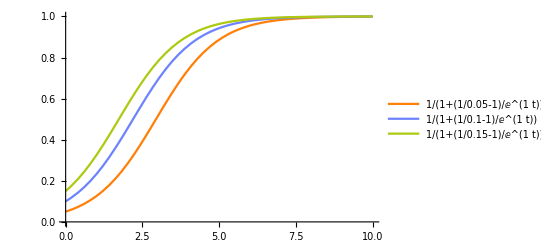

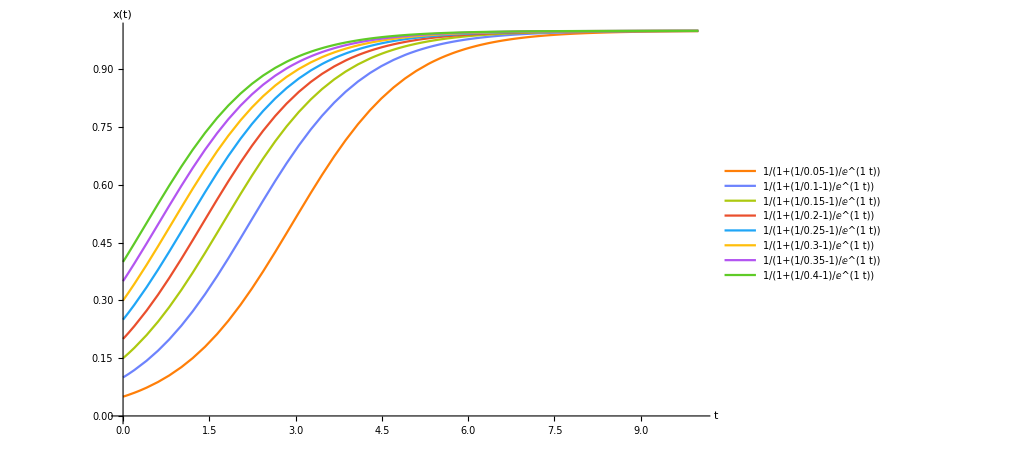

```mathematica
sig = Plot[{1/(1 + (1/0.05 - 1)/E^(1*t)), 1/(1 + (1/0.1 - 1)/E^(1*t)), 1/(1 + (1/0.15 - 1)/E^(1*t)), 1/(1 + (1/0.2 - 1)/E^(1*t)), 1/(1 + (1/0.25 - 1)/E^(1*t)), 
    1/(1 + (1/0.3 - 1)/E^(1*t)), 1/(1 + (1/0.35 - 1)/E^(1*t)), 1/(1 + (1/0.4 - 1)/E^(1*t))}, {t, 0, 10}, ImageSize -> 750, AxesLabel->{HoldForm[t],HoldForm[x[t]]},PlotLabel->None,LabelStyle->{GrayLevel[0]},AxesStyle->{Directive[Red,18],Directive[Red,18]}]
```

References

Weisstein, Eric W. “Logistic Equation.” From MathWorld--A Wolfram Web Resource. https://mathworld.wolfram.com/LogisticEquation.html. Accessed 11 April 2020.

Lerma, Miguel A. “Notes on Calculus II.” https://sites.math.northwestern.edu/~mlerma/courses/math214-2-04f/notes/c2-logist.pdf. Accessed 11 April 2020.